## Solar Flares & CMEs Problem Set 2 Roy Smart

```mathematica
Clear["Global`*"]
```

## Problem 2

```mathematica
N1vals = {A-> 2.75 10^6,b->0.95};
N1=A(r-b)^-2.38;
```

```mathematica
N2 = NB / r;
N2vals = {}
```

```mathematica
data=Transpose[Import["C:\\Users\\royts\\School\\Classes\\PHSX591_SolarFlaresAndCMEs\\ProblemSet_2\\p2_modelB.csv"]];
```

```mathematica
height = N[data[[1]] / 695700];
```

```mathematica
ne = data[[2]];
```

```mathematica
Transpose[{ne, height}]
```

{{8.29×10^8,0.00372431},{2.64×10^9,0.00337214},{4.1×10^9,0.00336064},{6.87×10^9,0.00334627},{9.07×10^9,0.00333765},{1.04×10^10,0.00333333},{1.21×10^10,0.00332758},{1.29×10^10,0.0033204},{1.34×10^10,0.0032974},{1.38×10^10,0.00327296},{1.44×10^10,0.00322697},{1.51×10^10,0.00316228},{1.58×10^10,0.00311197},{1.63×10^10,0.00308754},{1.71×10^10,0.00307316},{1.88×10^10,0.00306885},{2.31×10^10,0.0030631},{2.48×10^10,0.00306023},{2.6×10^10,0.00305448},{2.67×10^10,0.00302429},{2.69×10^10,0.00300848},{2.7×10^10,0.00298548},{2.72×10^10,0.00295817},{2.77×10^10,0.00291217},{2.84×10^10,0.00284605},{2.99×10^10,0.00275262},{3.38×10^10,0.00256576},{4.41×10^10,0.00230703},{5.43×10^10,0.00216329},{5.62×10^10,0.00198361},{6.02×10^10,0.00183987},{6.56×10^10,0.00173207},{7.06×10^10,0.00155239},{7.62×10^10,0.00140865},{7.55×10^10,0.00130085},{7.41×10^10,0.00122898},{6.38×10^10,0.00108524},{5.95×10^10,0.00101337},{6.88×10^10,0.000941498},{1.01×10^11,0.000869628},{1.61×10^11,0.000797758},{2.58×10^11,0.000725888},{4.31×10^11,0.000646831},{1.08×10^12,0.00050309},{2.65×10^12,0.00035935},{6.46×10^12,0.00021561},{1.07×10^13,0.00014374},{2.13×10^13,0.0000718701},{6.45×10^13,0.},{1.55×10^14,-0.000035935},{4.66×10^14,-0.0000718701},{1.21×10^15,-0.000107805}}

```mathematica
νp = 8.98 10^3 √ne;
```

```mathematica
plotdata=Transpose[{νp,height}];
```

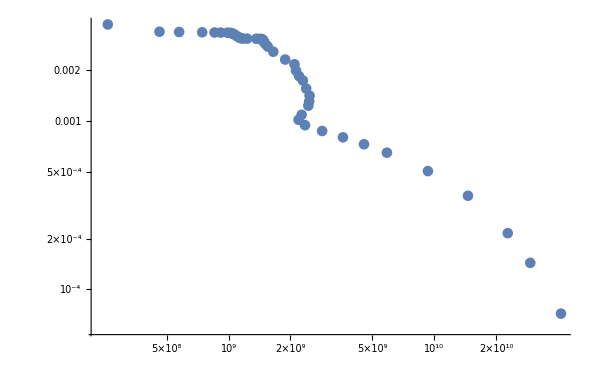

```mathematica
p2=ListLogLogPlot[plotdata]
```